```mathematica
f[x_,y_]:=y^2+x y+y-x^3-x^2+10x+10
```

Cambio de variable que simplifica la ecuación de Weierstrass:

```mathematica
Simplify[f[(x-15)/36,y/216-x/72-21/72]]
```

(263466+12987 x-x^3+y^2)/46656

```mathematica
F[x_,y_]:=y^2-x^3+12987 x+263466
```

Discriminante de la nueva ecuación simplificada:

```mathematica
Disc=4(-12987)^3+27(-263466)^2
```

-6887475360000

y su factorización:

```mathematica
FactorInteger[Disc]
```

{{-1,1},{2,8},{3,16},{5,4}}

Tres valores posibles para x para puntos de X_0(15) de la forma (x,0)

```mathematica
Solve[F[x,0]==0]
```

{{x→-102},{x→-21},{x→123}}

El conjunto de divisores, positivos y negativos, cuyos cuadrados dividen el discriminante

```mathematica
Divi=Union[Divisors[√-Disc],-Divisors[√-Disc]];
```

Vemos que divisores y_0, positivo o negativo, de √-Disc producen cúbicas de la forma F(x,y_0) que sí tiene soluciones racionales x.

```mathematica
DiviBuenos=Select[Divi,Length[Solve[F[x,#]==0,x,Integers]]>0&]
```

{-4860,-540,540,4860}

Producimos la tabla de soluciones:

```mathematica
Table[{Solve[F[x,y]==0,x,Integers],y},{y,DiviBuenos}]
```

{{{{x→303}},-4860},{{{x→-57}},-540},{{{x→-57}},540},{{{x→303}},4860}}

Por lo tanto el grupo de puntos racionales (distintos de O ) de la ecuación F es

```mathematica
G={{-102,0},{-21,0},{123,0},{303,-4860},{303,4860},{-57,-540},{-57,540}}
```

{{-102,0},{-21,0},{123,0},{303,-4860},{303,4860},{-57,-540},{-57,540}}

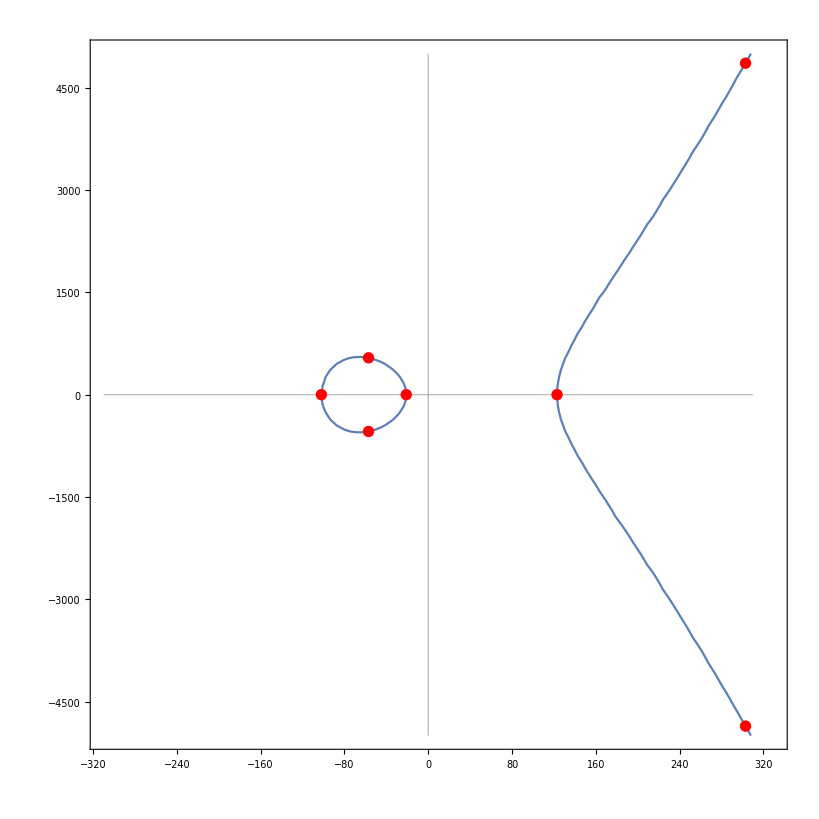

```mathematica
Show[ContourPlot[F[x,y]==0,{x,-310,330},{y,-5000,5000}],
Graphics[{Gray,Opacity[0.5],Line[{{-310,0},{310,0}}]}],
Graphics[{Gray,Opacity[0.5],Line[{{0,-5000},{0,5000}}]}],
Graphics[{Red,PointSize[.01],Point[G]}]
]
```

El cambio de coordenas a la ecuación de Weierstrass original es:

```mathematica
coord[{x_,y_}]:={(x-15)/36,y/216-x/72-21/72}
```

Bajo el cambio de coordenadas los puntos racionales de la ecuación simplificada se convierten en los puntos racionales de la ecuación de Weierstrass generalizada:

```mathematica
H=Table[coord[p],{p,G}]
```

```mathematica
{{-13/4,9/8},{-1,0},{3,-2},{8,-27},{8,18},{-2,-2},{-2,3}}
```

```mathematica
Simplify[F[36x+15,216 y+108 x+108]]
```

-46656 (-10+x^2+x^3-y-y^2-x (10+y))

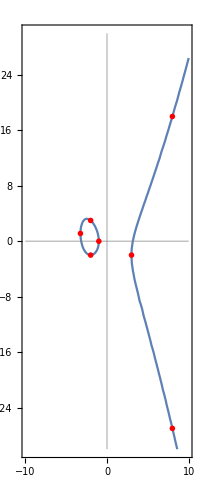

```mathematica
Show[ContourPlot[f[x,y]==0,{x,-10,10},{y,-30,30},AspectRatio->Automatic],
Graphics[{Gray,Opacity[0.5],Line[{{-10,0},{10,0}}]}],
Graphics[{Gray,Opacity[0.5],Line[{{0,-30},{0,30}}]}],
Graphics[{Red,PointSize[.01],Point[H]}]]
```

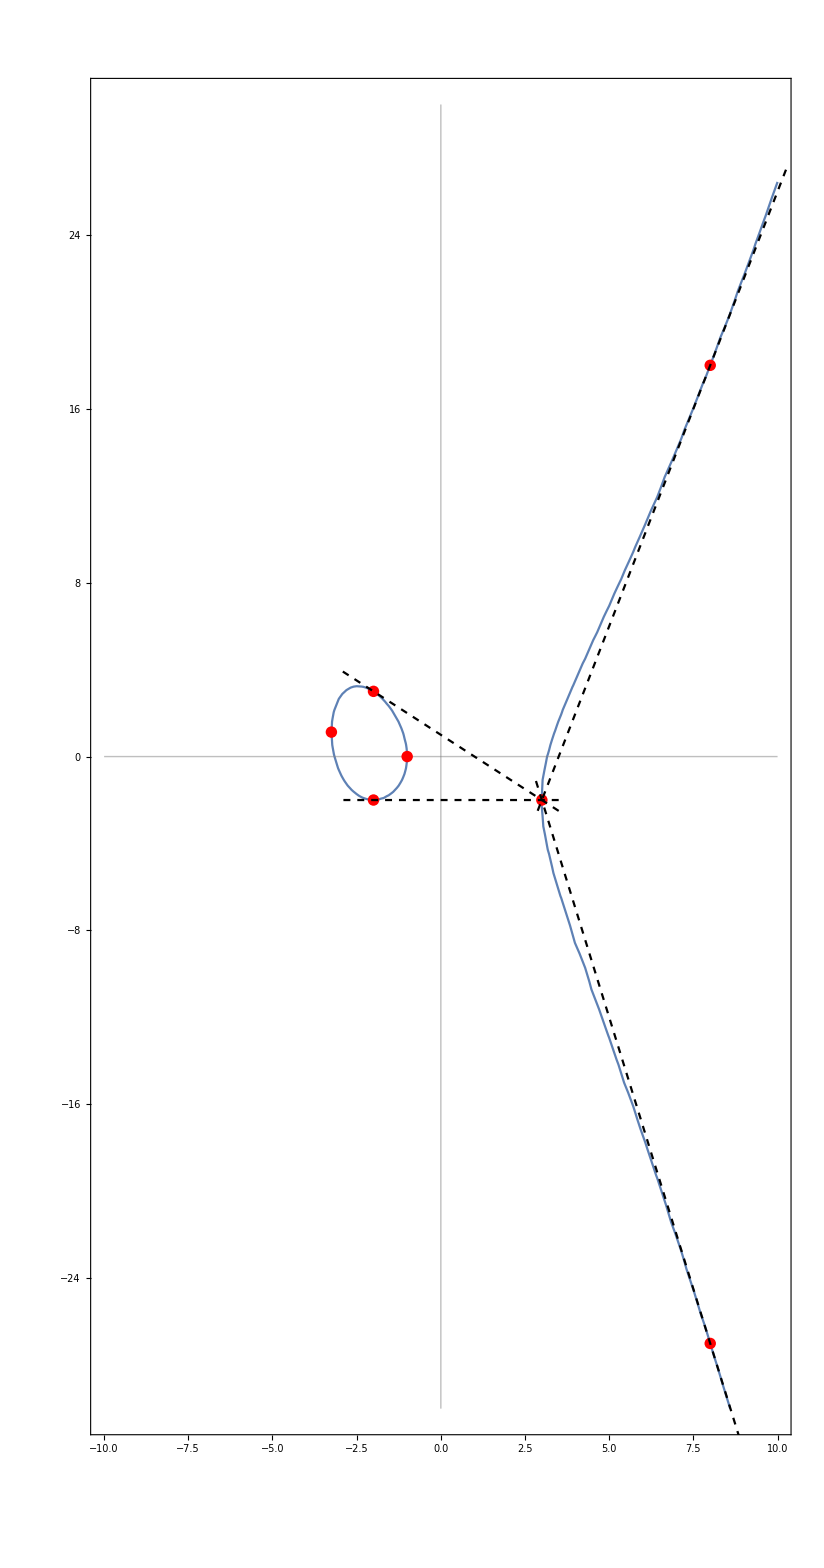

```mathematica
Show[ContourPlot[f[x,y]==0,{x,-10,10},{y,-30,30},AspectRatio->Automatic],
Graphics[{Gray,Opacity[0.5],Line[{{-10,0},{10,0}}]}],
Graphics[{Gray,Opacity[0.5],Line[{{0,-30},{0,30}}]}],
Graphics[{Red,PointSize[.01],Point[H]}],
ParametricPlot[{Derivative[0,1][f][-2,-2]t,Derivative[1,0][f][-2,-2]t}+{-2,-2},{t,-1.1,0.2},PlotStyle->{Black,Dashed}],
ParametricPlot[{-Derivative[1,0][f][-2,3]t,Derivative[0,1][f][-2,3]t}+{-2,3},{t,-1.1,0.2},PlotStyle->{Black,Dashed}],
ParametricPlot[{-Derivative[0,1][f][8,18]t,Derivative[1,0][f][8,18]t}+{8,18},{t,-.05,.115},PlotStyle->{Black,Dashed}],
ParametricPlot[{-Derivative[0,1][f][8,-27]t,Derivative[1,0][f][8,-27]t}+{8,-27},{t,-0.115,1},PlotStyle->{Black,Dashed}]
]
```

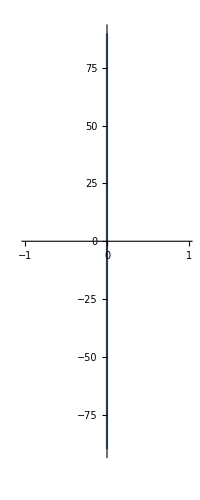

```mathematica
ParametricPlot[{Derivative[0,1][f][-1,0]t,Derivative[1,0][f][-1,0]t},{t,-10,10}]
```

```mathematica
Derivative[1,0][f][-1,0]
```

9

```mathematica
Derivative[0,1][f][-1,0]
```

0